23. Consider the following types of rules (see p.609).  A rule which accepts two arguments:  the first argument is a state which can be 0,1, or 2 and the second argument is an input which can be either {0,0}, {0,1}, {1,0} or {1,1}.  The output is a state, either 0,1,or2.

a) How many distinct rules are there that match the specification?

b) Write a function which takes a rule number and produces a rule.

c) Write a function which makes such a rule act on two binary lists of equal length, a Fold operation where the state changes according to the rule in which the second argument is the pair of binary (0 or 1) numbers from the same position in the two lists.   Take the initial state to be 0.

d.) Display the output of the rules acting on the x,y coordinates written in base 2, say on an array of size 64 by 64.  Try for instance the 36118th rule (with no convention, it is possible a different numbering scheme will behave differently).

e.) Make some measurements on a random sample to estimate the proportion of such rules which give a flip symmetry, and other sorts of symmetries.  (Possibly find more optimal ways of doing this.)

```mathematica
(* Answer a) Number of possible rules: 3 colors for the initial state, 4 different position for the new states, 3 colors for the new state *)
```

```mathematica
3^12
```

531441

```mathematica
(* I'll write a way to enumerate all the possible r.10ules: *)
```

```mathematica
IntegerDigits[483747,3,12]
```

{2,2,0,1,2,0,1,2,0,1,2,0}

```mathematica
(#-Mod[#,4])/4 & /@ Range[12]
```

{0,0,0,1,1,1,1,2,2,2,2,3}

```mathematica
(* posizione = Mod[m,4], stato = (m-posizione)/4, m è l'indice dell'array di 12 cifre in base 3 {0,1,2} che è associato alla rule number, dove le cifre {0,1,2} sono lo stato finale della trasformazione *)
```

```mathematica
(* posizione = Mod[m,4], stato = (m-posizione)/4, m is the index of the 12 digits array in base 3 {0,1,2} which represents the rule number, where the digits {0,1,2} are the final state of the transformation *)
```

```mathematica
{(#-Mod[#,4])/4,IntegerDigits[Mod[#,4],2,2]}->{IntegerDigits[483747,3,12][[#+1]]}& /@Range[0,11]
```

{{0,{0,0}}→{2},{0,{0,1}}→{2},{0,{1,0}}→{0},{0,{1,1}}→{1},{1,{0,0}}→{2},{1,{0,1}}→{0},{1,{1,0}}→{1},{1,{1,1}}→{2},{2,{0,0}}→{0},{2,{0,1}}→{1},{2,{1,0}}→{2},{2,{1,1}}→{0}}

```mathematica
(*rule number 292846*)
```

```mathematica
With[{regola=IntegerDigits[292846,3,12]},{(#-Mod[#,4])/4,IntegerDigits[Mod[#,4],2,2]}->{regola[[#+1]]}& /@Range[0,11]]
```

{{0,{0,0}}→{1},{0,{0,1}}→{1},{0,{1,0}}→{2},{0,{1,1}}→{2},{1,{0,0}}→{1},{1,{0,1}}→{2},{1,{1,0}}→{2},{1,{1,1}}→{0},{2,{0,0}}→{1},{2,{0,1}}→{0},{2,{1,0}}→{1},{2,{1,1}}→{1}}

```mathematica
(* Answer b *)
```

```mathematica
crearegola[n_Integer]:=If[n<3^12,With[{regola=IntegerDigits[n,3,12]},{(#-Mod[#,4])/4,IntegerDigits[Mod[#,4],2,2]}->{regola[[#+1]]}& /@Range[0,11]],Print["Rules number should be from 0 to 531441-1"]]
```

```mathematica
crearegola[399495]
```

{{0,{0,0}}→{2},{0,{0,1}}→{0},{0,{1,0}}→{2},{0,{1,1}}→{0},{1,{0,0}}→{2},{1,{0,1}}→{2},{1,{1,0}}→{0},{1,{1,1}}→{0},{2,{0,0}}→{0},{2,{0,1}}→{0},{2,{1,0}}→{1},{2,{1,1}}→{0}}

```mathematica
(* Question c) Write a function which makes such a rule act on two binary lists of equal length, a Fold operation where the state changes according to the rule in which the second argument is the pair of binary (0 or 1) numbers from the same position in the two lists.   Take the initial state to be 0. *)
```

```mathematica
(* Answer c *)
```

```mathematica
(*In this function I set the RULE for the next lines:*)
```

```mathematica
nuovostato[old_,{x_,y_}]:= With[{R= crearegola[398483]},Part[{old,{x,y}}/.R ,1]]
```

```mathematica
nuovostato[0,{0,0}]
```

2

```mathematica
(* I can either choose to generate at the beginning the two random arrays of {0,1} or to generate them when I Fold the "nuovostato" function over them,after I transposed them *)
```

```mathematica
dueliste[length_]:=FoldList[nuovostato[#1,#2]& ,0,Transpose[{RandomInteger[{0,1},length],RandomInteger[{0,1},length]}]]
```

```mathematica
dueliste[10]
```

{0,2,2,2,2,2,1,1,0,2,2}

```mathematica
(*just the final state:*)
```

```mathematica
duelistefinal[length_]:=Fold[nuovostato[#1,#2]& ,0,Transpose[{RandomInteger[{0,1},length],RandomInteger[{0,1},length]}]]
```

```mathematica
duelistefinal[10]
```

2

d.) Display the output of the rules acting on the x,y coordinates written in base 2, say on an array of size 64 by 64.  Try for instance the 36118th rule (with no convention, it is possible a different numbering scheme will behave differently).

```mathematica
(* In this section I use this global constant *)
```

```mathematica
$myrule=crearegola[36118]
```

crearegola[36118]

```mathematica
(* With this rule when a state becomes "1" it doesn't change anymore *)
```

```mathematica
crea[stato_]:= {stato,#}& /@ {{0,0},{0,1},{1,0},{1,1}}
```

```mathematica
(*this is the form of the initial state*)
```

```mathematica
crea[0]
```

{{0,{0,0}},{0,{0,1}},{0,{1,0}},{0,{1,1}}}

```mathematica
transform[stati_]:= Flatten[crea[#]/. $myrule&  /@ stati]
```

```mathematica
NestList[transform,{0},3]
```

{{0},{0,0,1,2},{0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1},{0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1}}

```mathematica
Length[Nest[transform,{0},3]]
```

64

```mathematica
64*64
```

4096

```mathematica
matrice[stati_]:= Module[{p={},d={},s=Partition[stati,2]},Table[If[EvenQ[i],AppendTo[p,s[[i]]],AppendTo[d,s[[i]]]],{i,Length[s]}];With[{L=Sqrt[Length[stati]]},Riffle[Partition[Flatten[d],L],Partition[Flatten[p],L]]]]
```

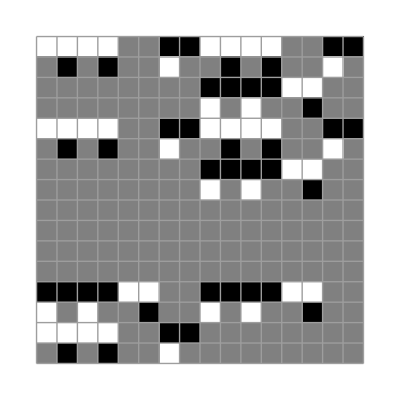

```mathematica
ArrayPlot[matrice[Nest[transform,{0},4]],Mesh->True]
```

```mathematica
(* In this way I display the 64x64 matrix (I have a global variable $myrule) *)
```

```mathematica
ArrayPlot[matrice[Nest[transform,{0},6]],Mesh->True]
```

-Graphics-

e.) Make some measurements on a random sample to estimate the proportion of such rules which give a flip symmetry, and other sorts of symmetries.  (Possibly find more optimal ways of doing this.)

```mathematica
(* In order to avoid global constants or variables I define a new function:*)
```

```mathematica
creagrafico[n_,steps_]:= With[{myrule=crearegola[n]},(transform[stati_]:= Flatten[crea[#]/. myrule &  /@ stati];ArrayPlot[matrice[Nest[transform,{0},steps]],Mesh->True])]
```

```mathematica
creagrafico[28743,6]
```

-Graphics-

```mathematica
creamatrice[n_,steps_]:= With[{myrule=crearegola[n]},(transform[stati_]:= Flatten[crea[#]/. myrule &  /@ stati];matrice[Nest[transform,{0},steps]])]
```

```mathematica
(* NOTE: FROM THE RULE 0 TO 6560 THE EVOLUTION IS TRIVIAL, IT MEANS THAT THE MATRIX REMAINS ALWAYS {0..}, FROM 6561 TO 6722 THE EVOLUTION CONTAINS {0,1}, FROM 6723 WE HAVE {0,1,2} AND THAN AGAIN JUST {0,1} and so on. That means that the evolution SWITCH FROM {0,1} OUTPUT, TO {0,1,2} OUTPUT. NON TRIVIAL RULES ARE FROM 6561 TO 531440. *)
```

```mathematica
(*For instance I'll try to find some rules that respect the symmetry for transposition*)
```

```mathematica
(*For few steps we can find symmetry, for more steps we don't. The qustion is: which rules respect this symmetry?*)
```

```mathematica
TakeWhile[Range[6561,6722],(creamatrice[#,2]== Transpose[creamatrice[#,2]])&]
```

{6561,6562,6563,6564,6565,6566,6567,6568,6569,6570,6571,6572,6573,6574,6575,6576,6577,6578,6579,6580,6581,6582,6583,6584,6585,6586,6587,6588,6589,6590,6591,6592,6593,6594,6595,6596,6597,6598,6599,6600,6601,6602,6603,6604,6605,6606,6607,6608,6609,6610,6611,6612,6613,6614,6615,6616,6617,6618,6619,6620,6621,6622,6623,6624,6625,6626,6627,6628,6629,6630,6631,6632,6633,6634,6635,6636,6637,6638,6639,6640,6641,6642,6643,6644,6645,6646,6647,6648,6649,6650,6651,6652,6653,6654,6655,6656,6657,6658,6659,6660,6661,6662,6663,6664,6665,6666,6667,6668,6669,6670,6671,6672,6673,6674,6675,6676,6677,6678,6679,6680,6681,6682,6683,6684,6685,6686,6687,6688,6689,6690,6691,6692,6693,6694,6695,6696,6697,6698,6699,6700,6701,6702,6703,6704,6705,6706,6707,6708,6709,6710,6711,6712,6713,6714,6715,6716,6717,6718,6719,6720,6721,6722}

```mathematica
TakeWhile[Range[6723,7289],(creamatrice[#,3]== Transpose[creamatrice[#,3]])&]
```

{}

```mathematica
(*I'll analyze (for 5 steps) the symmetry for Transposition in NON TRIVIAL rules. *)
```

```mathematica
(*The question is: How many rules respect a certain symmetry? *)
```

```mathematica
Length[TakeWhile[Range[6561,531440],(creamatrice[#,5]== Transpose[creamatrice[#,5]])&]]
```

0

```mathematica
(*The same but for the function Reverse (upside down each column)*)
```

```mathematica
Length[TakeWhile[Range[6561,531440],(creamatrice[#,5]== Reverse[creamatrice[#,5]])&]]
```

0

```mathematica
(* and also for reversing all raws *)
```

```mathematica
Length[TakeWhile[Range[6561,531440],(creamatrice[#,5]== Transpose[Reverse[Transpose[creamatrice[#,5]]]])&]]
```

0

```mathematica
(* This function evaluates the reflection of the matrix through the Y axes *)
```

```mathematica
YSymm[n_,steps_]:= With[{mm=(Partition[#,Length[#]/2]& )/@  creamatrice[n,steps]},Partition[Flatten[Riffle[Reverse[mm[[All,2]],2],Reverse[mm[[All,1]],2]]],Length[mm]]]
```

```mathematica
Length[TakeWhile[Range[6561,531440],(creamatrice[#,5]== YSymm[#,5])&]]
```

0

```mathematica
(* This function evaluates the reflection of the matrix through the X axes *)
```

```mathematica
XSymm[n_,steps_]:= With[{mm=creamatrice[n,steps]},Join[Reverse[mm[[(Length[mm]/2)+1;;Length[mm]]]],Reverse[mm[[1;;Length[mm]/2]]]]]
```

```mathematica
Length[TakeWhile[Range[6561,531440],(creamatrice[#,5]== XSymm[#,5])&]]
```

0